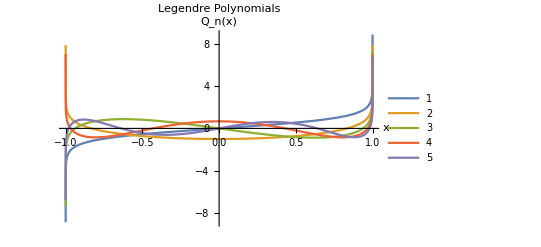

```mathematica
Plot[Evaluate[LegendreQ[Range[0,4],x]],{x,-1,1},PlotLegends->Automatic,PlotRange->All,AxesLabel->{"x","Q_n(x)"},PlotLabel->"Legendre Polynomials"]
```

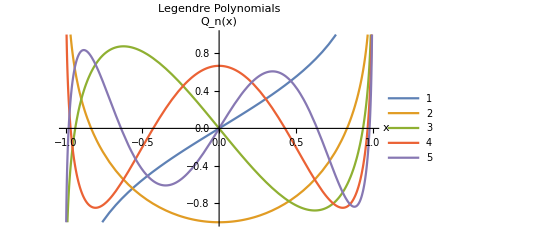

```mathematica
Plot[Evaluate[LegendreQ[Range[0,4],x]],{x,-1,1},PlotLegends->Automatic,PlotRange->{-1,1},AxesLabel->{"x","Q_n(x)"},PlotLabel->"Legendre Polynomials"]
```

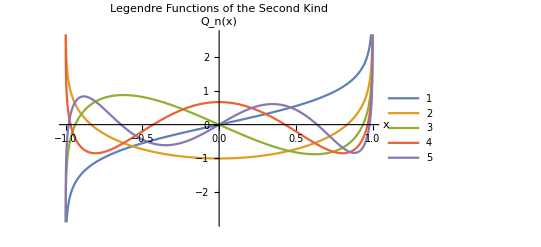

```mathematica
Plot[Evaluate[Table[LegendreQ[n,x],{n,0,4}]],{x,-1,1},PlotLegends->Automatic,AxesLabel->{"x","Q_n(x)"},PlotLabel->"Legendre Functions of the Second Kind"]
```

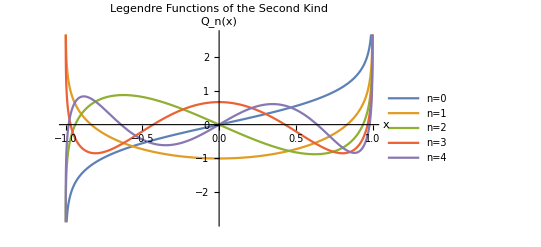

```mathematica
Plot[Evaluate[Table[LegendreQ[n,x],{n,0,4}]],{x,-1,1},PlotLegends->Table["n="<>ToString[n],{n,0,4}],AxesLabel->{"x","Q_n(x)"},PlotLabel->"Legendre Functions of the Second Kind"]
```

```mathematica
Plot[Evaluate[Table[LegendreQ[n,x],{n,0,4}]],{x,-1,1},PlotLegends->Table["n="<>ToString[n],{n,0,4}],AxesLabel->{"x","Q_n(x)"},PlotLabel->"Legendre Functions of the Second Kind",PlotRange->{{-1,1},Automatic}]
```

-Graphics-

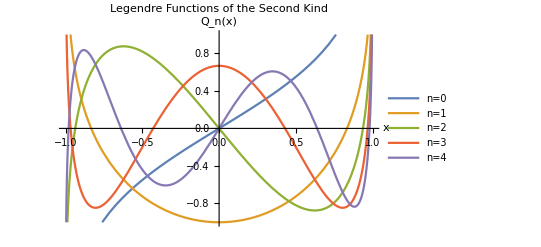

```mathematica
Plot[Evaluate[Table[LegendreQ[n,x],{n,0,4}]],{x,-1,1},PlotLegends->Table["n="<>ToString[n],{n,0,4}],AxesLabel->{"x","Q_n(x)"},PlotLabel->"Legendre Functions of the Second Kind",PlotRange->{{-1,1},{-1,1}}]
```